```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Chaozhi\Workspace\JuliaWorkspace\Workspace_Polyploid\PolyOrigin_Examples\tetraploid_simarray

```mathematica
localdisturb[geno_?MatrixQ,std_]:=Module[{nsnp,noise,bef,postorder,postgeno},
nsnp=Length[geno]-1;
If[std==0,noise=0,noise=RandomReal[NormalDistribution[0,std^2],nsnp]];
bef = Range[nsnp];
postorder=Ordering[bef+noise];
postgeno=geno[[Join[{1},1+postorder]]];
postgeno[[2;;,3]]=geno[[2;;,3]];
{postgeno,postorder}
]
```

```mathematica
localdisturb[dataid_?StringQ,std_]:=Module[{geno,postgeno,postorder,outfile,ls,tau,g},
geno=Import[dataid<>"geno.csv"];
{postgeno,postorder}= localdisturb[geno,std];
outfile=dataid<>"geno_disturbed.csv";
Export[outfile,postgeno];
ls={Range[Length[postorder]],postorder};
tau=N[KendallTau[Sequence@@ls]];
g=ListPlot[ls,PlotLabel->"tau="<>ToString[tau]];
{tau,outfile,g}
]
```

tetraploid_simarray_

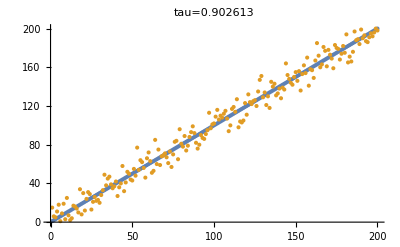
{0.902613,tetraploid_simarray_geno_disturbed.csv,-Graphics-}

```mathematica
dataid="tetraploid_simarray_"
localdisturb[dataid,3]
```